# Musical Game Of Life

## By Neamat Sabry

## The Problem

The Game of Life is a cellular automaton , “a discrete model composed of individual “cell - like” entities that perform a range of functions according to a predetermined set of coded instructions”, every cell in a finite grid has a status of alive or dead and its status in the following generation is determined by rules according to the number of neighbors around said cell.

My question: what if a cell could also hold a sound (maybe a pitch or a just a noise) so that when processed by some machine, the patterns produce music?

### How will this be helpful?

I am quite passionate about music and I like finding patterns in the songs I hear and pieces I play on my instrument. The Game Of Life is infamous for its patterns and I was itching to hear it in the form of notes rather than just black and white cells. With that. maybe we can:

Hear new interesting patterns with the sound we couldn’t otherwise see with our eyes in the visual Game Of Life

The  produced sound could be crated into a whole symphony of music!

### So the goal when starting this project was the following:

Represent each cell with a different sound so that when a play button is pressed, an assortment of sound of all live cells is created

Integrate mouse click interaction

Add more features like animation and the ability to use different instruments

## Overview of Techniques

I first used my Homework 6’s code for the Game of Life. Second, I added onto it click interaction using locator and create sound using Sound, SoundNote and EmitSound.

### First, sound in Mathematica

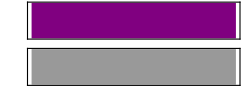

```mathematica
Sound[SoundNote["C"]]
```

```mathematica
-Graphics-;
```

```mathematica
Sound[SoundNote[0]]
```

-Graphics-

```mathematica
-Graphics-;
```

The only problem with is it has a few seconds of lag time.  I could use this too:

```mathematica
Play[Sin[2Pi 261.6256 t],{t,0,1}]
```

-Graphics-

But it requires calculating a wave function for all possible ranges of pitches and notes and it has less features (like using different instruments or easily playing around with chords). So I chose to work the Sound and represent notes with numbers rather than letters since they’re easier to manipulate.

### Second, the music conversion process

A music box, reading notes from left to right and playing notes on the same column/line at the same time.

Use this idea to read the Game Of Life grid from left to right, with varying notes and pitches going from low pitch (bottom) to higher pitch (top) where all live cells in the same column are played at the same time to create a chord.

```mathematica
-Graphics-;
```

These range of pitches will be created using the patterns of a major scale (2,2,1,2,2,2,1) or a chromatic e scale (1,1,1,1,1,1,1,1,1,1) (knowing that the difference between each notes and its lower/higher note is 12) and have it work for all grid sizes (up to a degree since we can’t have infinite pitches). This picture shows the process of creating notes for a selected Major scale and a 12*12 grid.

```mathematica
-Graphics-;
```

## Demo

### Graphics

```mathematica
bitGraphics[bitArray_,showPoints_]:=
Module[{colors,i,j,myDrawing,n},
n=Length[bitArray];
colors=ConstantArray[0,{n,n}];
myDrawing={EdgeForm[Directive[Thick,Cyan]]};
For[i=1,i≤  n,i++,
For[j=1,j≤   n,j++,
If[bitArray[[i,j]]==1 , colors[[i,j]]=Black];
If[bitArray[[i,j]]==0 , colors[[i,j]]=White];
AppendTo[myDrawing,colors[[i,j]]];
AppendTo[myDrawing, Rectangle[{j,-(i+1)}]];
If[showPoints,
AppendTo[myDrawing,Style[Text[{i,j},{j+0.5,(-(i+1))+0.5}],Red]]];
]];
myDrawing
]
```

### Code

#### Update bit array after click

```mathematica
updateBitArray[bitArray_,pt_,state_]:=
Module[{newBitArray,flrXCord,flrYCord,xCord,yCord},
{xCord,yCord}=pt;
flrXCord = Floor[xCord];
flrYCord=Floor[Abs[yCord]];
newBitArray = bitArray;
If[state==1,
newBitArray[[flrYCord,flrXCord]]=1];
If[state==0,
newBitArray[[flrYCord,flrXCord]]=0];
newBitArray
];
```

#### Calculate number of neighbors around current cell

```mathematica
nrOfNeighbors[a_,i_,j_]:=Module[{nrRows,nrCols,nr,neighbors={0}},
{nrRows,nrCols}=Dimensions[a];
Which[
(* center*)
i≥2 &&i<nrRows&&j≥2&&j<nrCols,
neighbors={
a[[i-1,j-1]],a[[i-1,j]],a[[i-1,j+1]],
a[[i,j-1]],a[[i,j+1]],
a[[i+1,j-1]],a[[i+1,j]],a[[i+1,j+1]]
},
(*corner top left *)
i==1&&j==1,
neighbors={a[[1,2]],a[[2,1]],a[[2,2]]},
(*corner top right *)
i==1&&j== nrCols,
neighbors={a[[1,j-1]],a[[2,j-1]],a[[2,j]]},
(*corner bottom left *)
i== nrRows&&j== 1,
neighbors={a[[i,2]],a[[i-1,1]],a[[i-1,2]]},
(*corner bottom right *)
i==nrRows&&j== nrCols,
neighbors={a[[i,j-1]], a[[i-1, j]],a[[i-1,j-1]]},
(*border top  *)
i==1 && j≥ 2 && j<nrCols,
neighbors={a[[1,j-1]],a[[1,j+1]],a[[2,j]],a[[2,j-1]],a[[2,j+1]]},
(*border bottom*)
i==nrRows && j≥ 2 && j<nrCols,
neighbors={a[[i,j-1]],a[[i,j+1]],a[[i-1,j]],a[[i-1,j-1]],a[[i-1,j+1]]},
(*border left*)
j==1 && i≥ 2 && i<nrRows,
neighbors={a[[i-1,1]],a[[i+1,1]],a[[i,2]],a[[i-1,2]],a[[i+1,2]]},
(*border right*)
j==nrCols && i≥ 2 && i <nrRows,
neighbors={a[[i-1,j]],a[[i+1,j]],a[[i,j-1]],a[[i-1,j-1]],a[[i+1,j-1]]}
];
nr=Total[neighbors]
];
```

#### Calculate status (whether dead or alive) in next generation for current cell

```mathematica
nextIJposiiton[a_,i_,j_]:=Module[{crtCell,cellStatus},
cellStatus=0;
crtCell = a[[i,j]];
Which[
(*if crtCell is alive and has 2 or 3 neighbors, then it will live*)
(crtCell== 1 && (nrOfNeighbors[a,i,j]==  3 || nrOfNeighbors[a,i,j]== 2)) , 
cellStatus=1,
(*if crtCell is alive and has more than 3 neighbors, it will die*)
crtCell== 1 && nrOfNeighbors[a,i,j] > 3 , 
cellStatus=0,
(*if crtCell is alive and has fewer than 2 neighbors, it will die*)
crtCell== 1 && nrOfNeighbors[a,i,j] < 2 , 
cellStatus=0,
(*if crtCell is dead and has exactly 3 neighbors, it will be reborn*)
crtCell== 0 && nrOfNeighbors[a,i,j]==  3, 
cellStatus=1
];
cellStatus
];
```

#### Compute Next Generation

```mathematica
nextGen[a_]:=Module[{newList,nrRows,nrCols,i,j,newA},
(*get dimensions of the grid*)
{nrRows,nrCols}=Dimensions[a];
(*redefine list a as newA*)
newList = a;
(*loop through cells in grid*)
For[i=1,i≤ nrRows,i++,
For[j=1,j≤ nrCols,j++,
newList[[i,j]]=nextIJposiiton[a,i,j];
];
];
newList
]
```

#### Convert grid to sound

```mathematica
convertToSound[bitArray_,scale_,instrument_]:=Module[{transpBitArr,sound,notesList,n,scaleLen,diff,u,upperIndex,lowerIndex,upperNote, lowerNote,isOdd},
n=Length[bitArray];
notesList={};
scaleLen=Length[scale];
(*checks for grid size and creates possible pitches accordingly using the chosen scale*)
Which[
(*if grid size is greater than 0 and less than or equal to 8, then the list of possible notes will be from the scale list from  0 up to that grid size *)
n≤ scaleLen && n> 0,
notesList=scale[[;;n]],
(*if the grid size is greater than 8, then it's going to be a bit complicated because we need to generate a list of notes according to the pattern of the scale pattern we have and the bigger grid size*)
n>scaleLen, 
(*as a base, we will append the 8 notes of the scale to the notesList. now notesList is 8 items long*)
notesList=scale;
(*then we will have diff -> the remainder of the gridsize - 8  to fill up with notes*)
diff=n-8;
(*if diff is odd, then it's going to cause a prolem later on, so make sure it's subtracted by 1 to make it even*)
If[OddQ[diff],
isOdd=True;
diff=diff-1;
];
(*then, instead of just adding more notes to the end of the list, i wanted to add more notes to the beginning and the end at teh same time so the notesList grows from both ends instead of one*)
(upperIndex=Length[notesList]-1;
lowerIndex=2;
For[u=1,u≤ (diff/2),u++,
(*we calculate the notes by finding the lowest and highest notes currently  in the list and add 12 to both to get the same notes but an octave higher/lower*)
upperNote=(notesList[[lowerIndex]]+12);
lowerNote=(notesList[[upperIndex]]-12);
AppendTo[notesList,upperNote];
PrependTo[notesList,lowerNote];
upperIndex=(upperIndex-1)+1;
lowerIndex+=2;
];
(*if diff was odd that means a subtracted a 1 earlier, so let's account for that by adding one more note*)
If[isOdd,
upperNote=(notesList[[lowerIndex]]+12);
AppendTo[notesList,upperNote]
]
)
];
(*tranpose the array so we have a list of columns instead of rows*)
transpBitArr=Transpose[bitArray];
(*pick will use the reverse (because we need the pitches from low to high) of notesList to map over the array*)
sound=Sound[SoundNote[#,1/6,instrument]&/@(Pick[Reverse[Flatten[notesList]],#,1]&/@transpBitArr)];
EmitSound[sound];
(*return the sound, notesList and the notes outputted to make the sound*)
{sound,notesList,(Pick[Reverse[Flatten[notesList]],#,1]&/@transpBitArr)}
];
```

### App

```mathematica
app[n_]:=DynamicModule[{bitArray,transpBitArray,sound,notesList,soundOutput},
(*exit exuection if grid is 0 or greater than 30*)
If[n==0 || n > 30,Print["You've inputed an invalid gridsize into the app. Exiting..."];Exit[]];
(*init bit array matrix of size n*)
bitArray=ConstantArray[0,{n,n}];
Manipulate[
(*if the points returned from locator are greater than 0, update the bit array*)
If[Length[pts]>0,
bitArray=updateBitArray[bitArray,pts[[1]],state];
pts={};
];
(*graph the array on a grid*)
Graphics[bitGraphics[bitArray,show],PlotRange->{{1,n+1},{-1,-(n+1)}}
],
(*locator click*)
{{pts,{}},Locator,LocatorAutoCreate->All,Appearance-> None},
(*state of the cell. black is alive and white is dead*)
Style["SET CELL TO",Bold,Black,12],
{{state,1,""},{1-> "BLACK",0-> "WHITE"}},
Delimiter,
(*show the {i,j} position of a cell in the matrix*)
Style["SHOW POINTS",Bold,Black,12],
{{show,False,""},{True, False}},
Delimiter,
(*set the scale to cmajor, blues or chromatic to be the default pattern of notes played*)
Style["SET SCALE",Bold,Black,12],
{{scale,{0,2,4,5,7,9,11,12},""},{{0,2,4,5,7,9,11,12}-> "CMAJOR",{0,3,5,6,7,10,11,12}-> "BLUES",{0,1,2,3,4,5,6,7,8,9,10,11,12}-> "CHROMATIC"}},
Delimiter,
(*set instrument*)
Style["INSTRUMENTS",Bold,Black,12],
{{instrument,"Piano",""},{"Accordion","Agogo","AltoSax","Applause",
"Atmosphere","Bagpipe","Bandoneon","Banjo","BaritoneSax","Bass","BassAndLead","Bassoon","Bird","BlownBottle","Bowed","BrassSection","Breath","Brightness","BrightPiano","Calliope","Celesta","Cello","Charang","Chiff","Choir","Clarinet","Clavi","Contrabass","Crystal","DrawbarOrgan","Dulcimer","Echoes",
"ElectricBass","ElectricGrandPiano","ElectricGuitar","ElectricPiano","ElectricPiano2","EnglishHorn","Fiddle","Fifths",
"Flute","FrenchHorn","FretlessBass","FretNoise","Glockenspiel","Goblins","Guitar","GuitarDistorted",
"GuitarHarmonics","GuitarMuted","GuitarOverdriven","Gunshot","Halo","Harmonica","Harp","Harpsichord",
"Helicopter","HonkyTonkPiano","JazzGuitar","Kalimba","Koto","Marimba","MelodicTom","Metallic",
"MusicBox","MutedTrumpet","NewAge","Oboe","Ocarina","OrchestraHit","Organ","PanFlute","PercussiveOrgan","Piano","Piccolo","PickedBass","PizzicatoStrings","Polysynth","Rain","Recorder",
"ReedOrgan","ReverseCymbal","RockOrgan","Sawtooth","SciFi","Seashore","Shakuhachi","Shamisen",
"Shanai","Sitar","SlapBass","SlapBass2","SopranoSax","Soundtrack","Square","Steeldrums",
"SteelGuitar","Strings","Strings2","Sweep","SynthBass","SynthBass2","SynthBrass","SynthBrass2","SynthDrum","SynthStrings","SynthStrings2","SynthVoice","Taiko","Telephone","TenorSax","Timpani",
"Tinklebell","TremoloStrings","Trombone","Trumpet","Tuba","TubularBells","Vibraphone","Viola",
"Violin","Voice","VoiceAahs","VoiceOohs",
"Warm","Whistle","Woodblock","Xylophone"}},
Delimiter,
(*generate next population*)
Button["NEXT",
bitArray=nextGen[bitArray]
],
Delimiter,
(*convert the generation of live cells into audible notes*)
Button["PLAY SOUND",
convertToSound[bitArray,scale,instrument]
],
Delimiter,
(*print the sound as well as the notes played*)
Button["PRINT SOUND",
{sound,notesList,soundOutput}=convertToSound[bitArray,scale,instrument];
Print["Sound ", sound," List of all possible notes: ",notesList, " Sound Ouput: ",soundOutput]],
Delimiter,
(*print the bit array matrx*)
Button["PRINT GAME",Print[bitArray]],
Delimiter,
(*create a random bit array matrix*)
Button["RANDOM",bitArray=RandomInteger[1,{n,n}];],
Delimiter,
(*reset to a bit array matrix of 0*)
Button["RESET",bitArray=ConstantArray[0,{n,n}]],
Delimiter,
ControlPlacement->Right
]
]
```

### Run

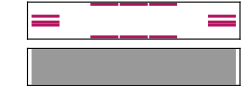
Sound -Graphics- List of all possible notes: {-3,-1,0,2,4,5,7,9,11,12,14,16} Sound Ouput: {{},{7,5,4},{},{11,0},{11,0},{11,0},{},{7,5,4},{},{},{},{}}

{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
app[12]
```

## Experimentation

So using my code, I decided to make it a continuous model with animation so I can hear the patterns in the sound.

### Conway’s Glider

The glider was the simplest and most interesting Game Of Life pattern to work with. As I have noticed, the glider only used three notes, usually a combination of a singular note, a minor and a third when using a chromatic scale, as it “glided” form higher pitch to lower pitch.

#### Animation App

```mathematica
appAnimate[gens_,initArray_,listOfNotes_]:=DynamicModule[{bitArray,show,i,arrList},
bitArray=initArray;
arrList={};
For[i=0,i≤ gens, i++,
AppendTo[arrList,bitArray];
bitArray=nextGen[bitArray]
];
Animate[
EmitSound[Sound[SoundNote[#,1/6,"Piano"]&/@(Pick[Reverse[listOfNotes],#,1]&/@Transpose[arrList[[Floor[u]]]])]];
Graphics[bitGraphics[arrList[[Floor[u]]],False],PlotRange->{{1,Length[bitArray]},{-1,-(Length[bitArray])}}],
{u,1,gens,1},AnimationRunning->False,AnimationRate-> 0.15
]
]
```

#### Run

```mathematica
INITARR={{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
NUMGENS=20;
LISTOFNOTES={0,2,4,5,7,9,11,12};
```

```mathematica
appAnimate[NUMGENS,INITARR,LISTOFNOTES];
```

When I stripped down the sound the glider makes to only singular notes, I found some interesting patterns.  Here’s an example of two generations of glider notes using sign waves to play the notes and the function Play

```mathematica
Off[General::spell1];
e4=Play[Sin[2Pi 329.64t],{t,0,0.4},DisplayFunction->Identity];
f4=Play[Sin[2Pi 349.24 t],{t,0,0.4},DisplayFunction->Identity];
g4=Play[Sin[2Pi 392.00 t],{t,0,0.4},DisplayFunction->Identity];
a4=Play[Sin[2Pi 440.00t],{t,0,0.4},DisplayFunction->Identity];
```

```mathematica
Show[{f4,a4,f4,g4,f4}]
```

-Graphics-

```mathematica
Show[{g4,f4,e4,g4,f4}]
```

-Graphics-

It sound  like a question the instal generation asked which is then answered so beautifully with the following generation’s notes.

### John Horton Conway

#### Run

```mathematica
INITARR2={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,1,1,1,0,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,1,1,1,0,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,0,0,1,0,0,0,0},{0,1,1,1,0,1,0,1,0,1,0,1,0,0,1,0,0,1,0,1,0,1,1,0,1,0,0,0,0},{0,1,0,1,0,1,0,1,0,1,0,0,0,0,1,0,0,1,0,1,0,1,0,1,1,0,0,0,0},{0,1,0,1,0,1,1,1,0,1,0,0,0,0,1,0,0,1,1,1,0,1,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,1,1,1,0,1,0,0,1,0,1,0,0,0,1,0,1,1,1,0,1,0,1,0},{0,0,1,0,0,0,1,0,1,0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,1,1,0},{0,0,1,0,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,1,1,1,0,0,0,1,0},{0,0,1,1,1,0,1,1,1,0,1,0,0,1,0,1,1,0,1,1,0,1,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
NUMGENS2=100;
LISTOFNOTES2={-17,-15,-13,-12,-10,-8,-7,-5,-3,-1,0,2,4,5,7,9,11,12,14,16,17,19,21,23,24,26,28,29,31};
```

```mathematica
appAnimate[NUMGENS2,INITARR2,LISTOFNOTES2];
```

### One more experiment

```mathematica
INITARR3={{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,1,1,0,0,0},{0,0,1,0,1,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
```

```mathematica
appAnimate[NUMGENS,INITARR3,LISTOFNOTES];
```

### Bootstrapping outputted list of notes (failed experiment)

```mathematica
Sound[SoundNote[#]&/@{{13,9,5,2,0},{15,12,7,5,4,2,0},{15,13,11,7,5,4},{15,13,9,7,4,2,0},{15,13,12,11,5,4},{12,9,7,4},{12,11,9,2},{11,7,5,0},{13,12,11,9,4,2},{15,12,7,4,2}}];
```

```mathematica
Flatten[{{13,9,5,2,0},{15,12,7,5,4,2,0},{15,13,11,7,5,4},{15,13,9,7,4,2,0},{15,13,12,11,5,4},{12,9,7,4},{12,11,9,2},{11,7,5,0},{13,12,11,9,4,2},{15,12,7,4,2}}]
```

{13,9,5,2,0,15,12,7,5,4,2,0,15,13,11,7,5,4,15,13,9,7,4,2,0,15,13,12,11,5,4,12,9,7,4,12,11,9,2,11,7,5,0,13,12,11,9,4,2,15,12,7,4,2}

```mathematica
data={13,9,5,2,0,15,12,7,5,4,2,0,15,13,11,7,5,4,15,13,9,7,4,2,0,15,13,12,11,5,4,12,9,7,4,12,11,9,2,11,7,5,0,13,12,11,9,4,2,15,12,7,4,2}
```

{13,9,5,2,0,15,12,7,5,4,2,0,15,13,11,7,5,4,15,13,9,7,4,2,0,15,13,12,11,5,4,12,9,7,4,12,11,9,2,11,7,5,0,13,12,11,9,4,2,15,12,7,4,2}

```mathematica
MeanAround[{13,9,5,2,0,15,12,7,5,4,2,0,15,13,11,7,5,4,15,13,9,7,4,2,0,15,13,12,11,5,4,12,9,7,4,12,11,9,2,11,7,5,0,13,12,11,9,4,2,15,12,7,4,2}]
```

7.80.6

```mathematica
ListPlay[Table[Skewness[RandomChoice[data,Length[data]]],{10000}]]
```

-Graphics-

(the above code was taken from Mathematica https://reference.wolfram.com/language/howto/PerformABootstrapAnalysis.html)

## What I Learned

Different sound functions in Mathematica

Locator

Pick function

&/@ with #

Animation

Many more...

## Future Work

Make it more efficient

Different colored cells to represent different instruments and thus play an orchestra of sound

Have more scales available

Include more features, like adding labels for the pitch a cell contains

A rectangular n*n grid

## References

Mathematica documentation, first and foremost.

Game Of Life

“Conway’s Game of Life.” Wikipedia, Wikimedia Foundation, 21 Apr. 2020, en.wikipedia.org/wiki/Conway%27s_Game_of_Life.
https://www.youtube.com/watch?v=R9Plq-D1gEk&t=266s

Originally inspired by Mathematica demo

https://demonstrations.wolfram.com/MusicFromTheGameOfLife/

Game of life and modelling
Hibbert, Chloe. “Conway’s Game of Life and the Birth of Agent-Based Modeling.” Simudyne, 2 Aug. 2019, www.simudyne.com/resources/conways-game-of-life-and-the-birth-of-agent-based-modeling/.

Game of life and music

“Game of Life Music Synthesizer.” Game of Life Music Synthesizer, people.ece.cornell.edu/land/courses/ece5760/FinalProjects/f2011/lba36_wl336/lba36_wl336/index.html.

https://www.youtube.com/watch?v=x22zysfrVSk&t=2s

https://www.youtube.com/watch?time_continue=14&v=avK-BmL2KZ4&feature=emb_log

Turning notes into sign waves and making music (downloadable notebook)
https://library.wolfram.com/infocenter/MathSource/5168/MathematicaMusic.nb?file_id=4892

Folding Space-Time https://www.youtube.com/watch?v=WkmPDOq2WfA&t=3s

## Thank you! Questions? Suggestions? Concerns?

```mathematica
INITARR4={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,1,0,1,0,1,1,1,0,1,0,0,1,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,1,1,0,1,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,1,0,1,1,1,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,1,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
appAnimate[NUMGENS2,INITARR4,LISTOFNOTES2];
```